```mathematica
`Private`PainleveIINegative["HMNeg"] =`HastingsMcLeodNegative`PainleveIIHMNeg;
Begin["`HastingsMcLeodNegative`"];
```

## Routine

```mathematica
β[y_,λ_]:=((λ-y)/(λ+y))^(1/4);
βp[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,0];
βm[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,-2π];
Y[{σ_,y_},λ_]:=1/2({{β[y,λ]+β[y,λ]^(-1), -σ (β[y,λ]-β[y,λ]^(-1))}, {-σ (β[y,λ]-β[y,λ]^(-1)), β[y,λ]+β[y,λ]^(-1)}});
Yp[{σ_,y_},λ_]:=1/2({{βp[y,λ]+βp[y,λ]^(-1), -σ (βp[y,λ]-βp[y,λ]^(-1))}, {-σ (βp[y,λ]-βp[y,λ]^(-1)), βp[y,λ]+βp[y,λ]^(-1)}});
Ym[{σ_,y_},λ_]:=1/2({{βm[y,λ]+βm[y,λ]^(-1), -σ (βm[y,λ]-βm[y,λ]^(-1))}, {-σ (βm[y,λ]-βm[y,λ]^(-1)), βm[y,λ]+βm[y,λ]^(-1)}});
σ3=({{1, 0}, {0, -1}});
Σ=({{0, I}, {I, 0}});

g[_,_?InfinityQ]:=∞;
g[y_,z_]:=I 4/3 (z+y)^(3/2)(z-y)^(3/2);
gp[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,0];
gm[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,-2π];
θ[x_,z_]:=4 I/3z^3+I x z;
Φ[{σ_,y_},z_]:=Y[{σ,y},z].MatrixExp[(-g[y,z]) σ3];
Φp[{σ_,y_},z_]:=Yp[{σ,y},z].MatrixExp[-(gp[y,z]) σ3];
Φm[{σ_,y_},z_]:=Ym[{σ,y},z].MatrixExp[-(gm[y,z]) σ3];
```

```mathematica
Clear[GGΣ,GGΣin,GG,S];
S[s_,k_?EvenQ]:=({{1, s[k]}, {0, 1}});
S[s_,k_?OddQ]:=({{1, 0}, {s[k], 1}});
GGΣ[_][_,_?InfinityQ]:=IdentityMatrix[2];
GGΣ[{s_,y_}][z_]=Φm[{s[1]I,y},z].Inverse[S[s,1]].Inverse[Φm[{s[1]I,y},z]];
GGΣin[{s_,y_}][z_]=GGΣ[{s,y}][z]//Inverse;
GG[_,_][_?InfinityQ]:=IdentityMatrix[2];
GG[{s_,y_},6][z_]=Φ[{s[1]I,y},z].S[s,6].Inverse[Φ[{s[1]I,y},z]];
GG[{s_,y_},1][z_]=Φ[{s[1]I,y},z].S[s,1].Inverse[Φ[{s[1]I,y},z]];
GG[{s_,y_},3][z_]=Φ[{s[1]I,y},z].S[s,3].Inverse[Φ[{s[1]I,y},z]];
GG[{s_,y_},4][z_]=Φ[{s[1]I,y},z].S[s,4].Inverse[Φ[{s[1]I,y},z]];
```

```mathematica
GLC[{s_,y_},1][z_]=Inverse[Φm[{s[1]I,y},z]];
GLC[{s_,y_},2][z_]=S[s,6].S[s,1].S[s,3].Inverse[Φ[{s[1]I,y},z]];
GLC[{s_,y_},3][z_]=S[s,6].S[s,1].Inverse[Φp[{s[1]I,y},z]];
```

```mathematica
GRC[{s_,y_},1][z_]=S[s,6].S[s,1].Inverse[Φp[{s[1]I,y},z]];
GRC[{s_,y_},2][z_]=S[s,6].Inverse[Φ[{s[1]I,y},z]];
GRC[{s_,y_},3][z_]=Inverse[Φm[{s[1]I,y},z]];
```

```mathematica
Ψpin[{σ_,y_},z_]=Inverse[Φp[{σ,y},z]];
GMid[{s_,y_}][z_]=Φp[{s[1]I,y},z].S[s,2].Ψpin[{s[1]I,y},z];
```

```mathematica
rngg={.5,2.3};

Cdefs[n_]:={{Function[y,({{-y, y}, {y, -y}})],({{Line[{.5,4}], n}, {Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n+5}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n+5}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n+5}})},
{Function[y,({{0}, {Sqrt[y]}})],({{Line[2 {-I,I}], 6}})}};
Gl[y_]:={({{GGΣ[y], GGΣin[y]}, {GG[y,3], GG[y,6]}, {GG[y,4], GG[y,1]}, {GLC[y,1], GRC[y,1]}, {GLC[y,2], GRC[y,2]}, {GLC[y,3], GRC[y,3]}}),{{GMid[y]}}};
```

```mathematica
ΦθSeries[s1_,x_]:=I s1 Sqrt[-x/2]/2 ;
slv//Clear;slv[n_]:=slv[n]=ScaledRHSolver[Cdefs[n]];

PainleveIIHMNeg[sin_,x_]:=Module[{s,y,n},
y=Sqrt[-x/2];
n=30;
{s[1],s[2],s[3]}=sin;
{s[4],s[5],s[6]}=-Array[s,3];
2 ΦθSeries[s[1],x]-1/(π I)Total[DomainIntegrate/@slv[n][Sqrt[-x/2],Gl[{s,Sqrt[-x/2]}]]]⟦1,2⟧
]
```

## Testing

```mathematica
data=Partition[ReadList["RiemannHilbert/Data/McLeodSolution.txt",Number],7];
```

```mathematica
Select[data,First[#]==-8.5&]
```

```mathematica
2.061129983899231-2.061129983888335
```

1.08962×10^-11

```mathematica
Sqrt[-8.5/2]
```

```mathematica
0.+2.0615528128088303 ⅈ
```

```mathematica
{{-8.5,12.03108999539436,-2.061129983888335,0.1213933475295986,2.487494132315518,0.7232543682788083,-2.108719199802199}}
```

```mathematica
PainleveIIHMNeg[{I,2.,-I},-8.6]//Timing
```

{1.98458,-2.07323+2.00773×10^-15 ⅈ}

```mathematica
PainleveII[{I,2.,-I},-8.6]//Timing
```

```mathematica
{7.588818000000018,-2.0732335913103896-4.969616689786745*^-17 ⅈ}
```

```mathematica
PainleveIIHMNeg[{I,0.,-I},-8.5]
```

```mathematica
-2.0611299838911834+2.0022033463518598*^-15 ⅈ
```

```mathematica
-2.0611299838912633+2.8830679046165605*^-15 ⅈ
```

```mathematica
PainleveIIHMNeg[{I,2.,-I},-8.5]
```

```mathematica
-2.061129983899231+2.0022033463518598*^-15 ⅈ
```

```mathematica
-2.061129983899311+2.8830679046165605*^-15 ⅈ
```

```mathematica
PainleveIIHMNeg[{I,2.,-I},-8.1]
```

```mathematica
-2.011983613757918-5.179444950022185*^-16 ⅈ
```

```mathematica
PainleveII[{I,2.,-I},-8.5]
```

```mathematica
-2.06112997399031-4.779114716678253*^-16 ⅈ
```

```mathematica
-2.011983607120466-9.376010154730993*^-16 ⅈ
```

```mathematica
{s[1],s[2],s[3]}={I,2.,-I};
{s[4],s[5],s[6]}=-Array[s,3];
```

```mathematica
x=-8.5;
```

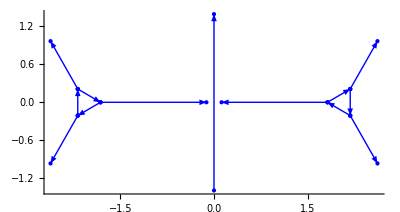

```mathematica
ConstructCurve[Cdefs[25],Gl[{s,Sqrt[-x/2]}],Sqrt[-x/2]]//DomainPlot
```

```mathematica
ConstructCurve[Cdefs[25],Gl[{s,Sqrt[-x/2]}],Sqrt[-x/2]]⟦1⟧//Last
```

{{1.+0. ⅈ,2.37095×10^-12-4.02364×10^-11 ⅈ},{-2.37095×10^-12-4.02364×10^-11 ⅈ,1.+0. ⅈ}}

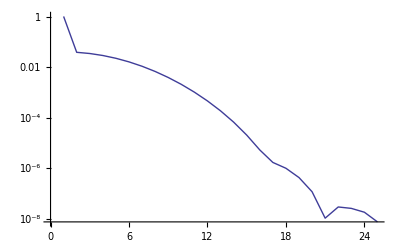
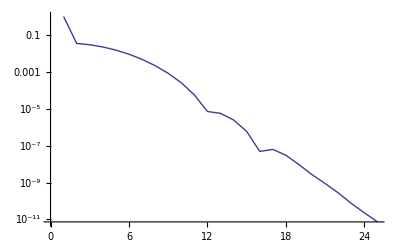
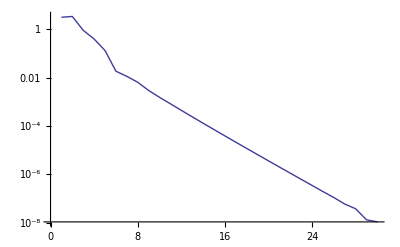
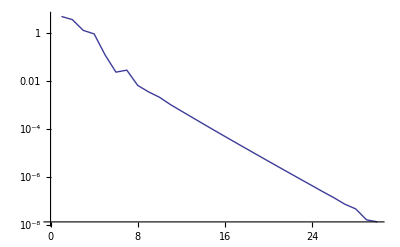
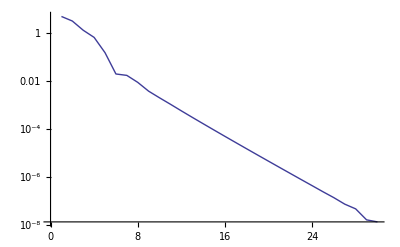
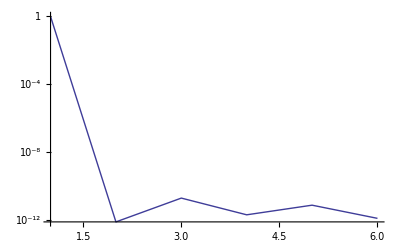
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DCTPlot/@ConstructCurve[Cdefs[25],Gl[{s,Sqrt[-x/2]}],Sqrt[-x/2]]
```

```mathematica
slv[25][Sqrt[-x/2],Gl[Sqrt[-x/2]]]
```

$Aborted

```mathematica
PainleveII[{I,2.,-I},-8.]
```

```mathematica
.
```

## Close

```mathematica
End[]
```